# Master’s Thesis Work

By Bora Basyildiz

## Ashabb Coupling Hamiltonian

```mathematica
SubMinus[σ] = {{0,0,0},{1,0,0},{0,√2,0}};SubPlus[σ] = ConjugateTranspose[SubMinus[σ]];H =KroneckerProduct[SubPlus[σ]+SubMinus[σ],SubPlus[σ]+SubMinus[σ]];Eigenvalues[H]
```

{-3,-3,3,3,0,0,0,0,0}

```mathematica
SubMinus[σ] = {{0,0,0},{1,0,0},{0,1,0}};SubPlus[σ] = ConjugateTranspose[SubMinus[σ]];H =KroneckerProduct[SubPlus[σ]+SubMinus[σ],SubPlus[σ]+SubMinus[σ]];Eigenvalues[H]
```

{-2,-2,2,2,0,0,0,0,0}

```mathematica
KroneckerProduct[SubPlus[σ],SubMinus[σ]] + KroneckerProduct[SubMinus[σ],SubPlus[σ]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | √2 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | √2 | 0 | 0 | 0 | √2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | √2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
H0=({{0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 1, 0, 0, 0, 1, 0, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0}}); Norm[H,"Frobenius"];Eigenvalues[H0]
```

{-2,2,0,0,0,0,0,0,0}

```mathematica
Max[Eigenvalues[H]]
```

3

```mathematica
SubMinus[σ] = {{0,0,0},{1,0,0},{0,1,0}};SubPlus[σ] = ConjugateTranspose[SubMinus[σ]];H =KroneckerProduct[SubPlus[σ]+SubMinus[σ],SubPlus[σ]+SubMinus[σ]];Eigenvalues[H]
```

{-2,-2,2,2,0,0,0,0,0}

```mathematica
SubMinus[σ] = ({{0, 0, 0, 0}, {1, 0, 0, 0}, {0, √2, 0, 0}, {0, 0, √3, 0}});SubPlus[σ] = ConjugateTranspose[SubMinus[σ]];H =KroneckerProduct[SubPlus[σ]+SubMinus[σ],SubPlus[σ]+SubMinus[σ]];Max[Eigenvalues[H]]
```

3+√6

```mathematica
SubMinus[σ] = ({{0, 0, 0, 0}, {1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}});SubPlus[σ] = ConjugateTranspose[SubMinus[σ]];H =KroneckerProduct[SubPlus[σ]+SubMinus[σ],SubPlus[σ]+SubMinus[σ]];Max[Eigenvalues[H]]
```

1/2 (3+√5)

```mathematica
SubMinus[σ] = ({{0, 0, 0, 0, 0}, {1, 0, 0, 0, 0}, {0, √2, 0, 0, 0}, {0, 0, √3, 0, 0}, {0, 0, 0, 2, 0}});SubPlus[σ] = ConjugateTranspose[SubMinus[σ]];H =KroneckerProduct[SubPlus[σ]+SubMinus[σ],SubPlus[σ]+SubMinus[σ]];Max[Eigenvalues[H]]
```

5+√10

```mathematica
SubMinus[σ] = ({{0, 0, 0, 0, 0}, {1, 0, 0, 0, 0}, {0, 1, 0, 0, 0}, {0, 0, 1, 0, 0}, {0, 0, 0, 1, 0}});SubPlus[σ] = ConjugateTranspose[SubMinus[σ]];H =KroneckerProduct[SubPlus[σ]+SubMinus[σ],SubPlus[σ]+SubMinus[σ]];Max[Eigenvalues[H]]//N
```

3.

```mathematica
SubMinus[σ] = ({{0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0}, {0, √2, 0, 0, 0, 0}, {0, 0, √3, 0, 0, 0}, {0, 0, 0, 2, 0, 0}, {0, 0, 0, 0, √5, 0}});SubPlus[σ] = ConjugateTranspose[SubMinus[σ]];H =KroneckerProduct[SubPlus[σ]+SubMinus[σ],SubPlus[σ]+SubMinus[σ]];Max[Eigenvalues[H]]
```

Root11.1Root[-15+45 #1-15 #1^2+#1^3&,3]11.05068748452652

```mathematica
SubMinus[σ] = ({{0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0}, {0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 1, 0}});SubPlus[σ] = ConjugateTranspose[SubMinus[σ]];H =KroneckerProduct[SubPlus[σ]+SubMinus[σ],SubPlus[σ]+SubMinus[σ]];Max[Eigenvalues[H]]//N
```

3.24698

```mathematica
Eigenvalues[mat]
```

{-√2,√2,0}

```mathematica
MatrixForm[{{0,0,0},{1,0,0},{0,1,0}}]
```

(0 | 0 | 0
1 | 0 | 0
0 | √2 | 0)

```mathematica
SubPlus[σ] = ConjugateTranspose[SubMinus[σ]]
```

{{0,1,0},{0,0,1},{0,0,0}}

```mathematica
MatrixForm[{{0,1,0},{0,0,√2},{0,0,0}}]
```

(0 | 1 | 0
0 | 0 | √2
0 | 0 | 0)

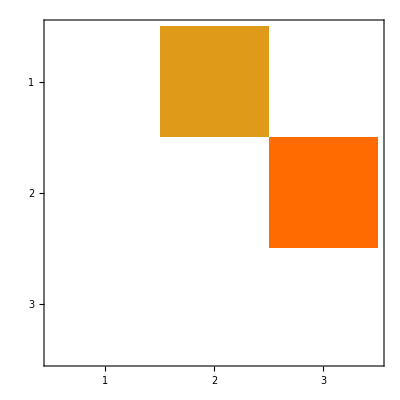

```mathematica
MatrixPlot[{{0,1,0},{0,0,√2},{0,0,0}}]
```

```mathematica
H =KroneckerProduct[SubPlus[σ]+SubMinus[σ],SubPlus[σ]+SubMinus[σ]];
```

```mathematica
H//MatrixForm
```

(0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0)

```mathematica
Eigenvalues[H]
```

{-2,-2,2,2,0,0,0,0,0}

```mathematica
Tr[H.H]
```

16

```mathematica
KroneckerProduct[SubPlus[σ]+SubMinus[σ],SubPlus[σ]+SubMinus[σ]]//MatrixForm
```

(0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0)

```mathematica
({{0, 1, 0}, {1, 0, 0}, {0, 0, 0}})//Eigenvalues
```

{-1,1,0}

```mathematica
A = KroneckerProduct[SubPlus[σ]+SubMinus[σ],SubPlus[σ]+SubMinus[σ]]//MatrixForm
```

(0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | √2 | 0 | 0 | 0
0 | 0 | 0 | 0 | √2 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | √2 | 0
1 | 0 | √2 | 0 | 0 | 0 | √2 | 0 | 2
0 | √2 | 0 | 0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | √2 | 0 | 0 | 0 | 0
0 | 0 | 0 | √2 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0)

```mathematica
psi = {{0,1,0,0,0,0,0,0,0}}
```

{{0,1,0,0,0,0,0,0,0}}

```mathematica
psi//MatrixForm
```

```mathematica
A
```

(0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | √2 | 0 | 0 | 0
0 | 0 | 0 | 0 | √2 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | √2 | 0
1 | 0 | √2 | 0 | 0 | 0 | √2 | 0 | 2
0 | √2 | 0 | 0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | √2 | 0 | 0 | 0 | 0
0 | 0 | 0 | √2 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0)

```mathematica
Transpose[{{0,1,0,0,0,0,0,0,0}}]//MatrixForm
```

(0
1
0
0
0
0
0
0
0)

```mathematica
psi.A.A.Transpose[psi]
```

{{0,1,0,0,0,0,0,0,0}}.(0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | √2 | 0 | 0 | 0
0 | 0 | 0 | 0 | √2 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | √2 | 0
1 | 0 | √2 | 0 | 0 | 0 | √2 | 0 | 2
0 | √2 | 0 | 0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | √2 | 0 | 0 | 0 | 0
0 | 0 | 0 | √2 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0).(0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | √2 | 0 | 0 | 0
0 | 0 | 0 | 0 | √2 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | √2 | 0
1 | 0 | √2 | 0 | 0 | 0 | √2 | 0 | 2
0 | √2 | 0 | 0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | √2 | 0 | 0 | 0 | 0
0 | 0 | 0 | √2 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0).{{0},{1},{0},{0},{0},{0},{0},{0},{0}}

```mathematica
({{□, □, □}}
```

## Ray Coupling Hamiltonian